```mathematica
ReadPlantri[fileName_]:=Block[{file,vertices,result={},header,i, next,v, bigresult={}},
PrintTemporary["Reading " <> fileName];
file=OpenRead[fileName,BinaryFormat->True];
(* read header *)
For[i=1,i≤StringLength[">>planar_code<<"],i++,
header=BinaryRead[file];
];
vertices=BinaryRead[file];
While[vertices=!=EndOfFile,
result={};
For[v=1,v≤vertices,v++,
next=BinaryRead[file];
While[next ≠ 0,
result=Append[result,If[v<next,v<->next,next<->v]];
next=BinaryRead[file];
];
];
bigresult=Append[bigresult,Sort[DeleteDuplicates[result]]];
vertices=BinaryRead[file];
];
Close[file];
PrintTemporary["Done. " <> ToString[Length[bigresult]]];
bigresult
]
```

```mathematica
pl=ReadPlantri["D:\\cygwin64\\home\\alfre\\groph.txt"];Length[pl]
```

7595

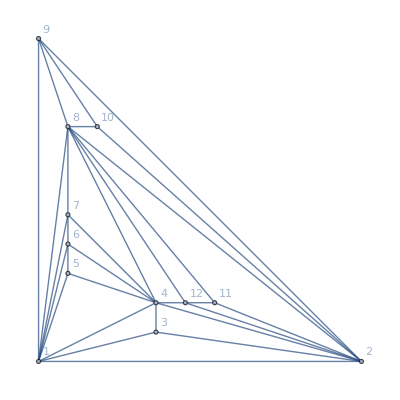

```mathematica
g23=Graph[pl[[1]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```

```mathematica
Table[ChromaticPolynomial[Graph[edges,GraphLayout->"PlanarEmbedding", VertexLabels->"Name"],x]//CompleteBaseCoeff,{edges,pl}]//Tally//Sort
```

{{{0,0,0,0,1,63,301,350,140,21,1},93},{{0,0,0,0,2,104,396,395,145,21,1},3},{{0,0,0,0,3,113,394,389,144,21,1},17},{{0,0,0,0,4,100,357,371,142,21,1},57},{{0,0,0,0,5,115,382,381,143,21,1},29},{{0,0,0,0,5,130,425,405,146,21,1},1},{{0,0,0,0,6,123,415,403,146,21,1},1},{{0,0,0,0,6,128,415,398,145,21,1},5},{{0,0,0,0,7,154,448,409,146,21,1},1},{{0,0,0,0,8,123,411,402,146,21,1},1},{{0,0,0,0,9,145,428,400,145,21,1},4},{{0,0,0,0,11,178,467,412,146,21,1},1},{{0,0,0,0,12,154,422,393,144,21,1},9},{{0,0,0,0,13,153,439,407,146,21,1},1},{{0,0,0,0,14,160,445,408,146,21,1},2},{{0,0,0,0,16,153,417,392,144,21,1},4},{{0,0,0,0,20,175,444,402,145,21,1},1},{{0,0,0,0,21,203,469,406,145,21,1},1},{{0,0,0,1,27,191,465,411,146,21,1},1},{{0,0,0,1,43,273,525,420,146,21,1},1}}

```mathematica
pl2=Select[pl,CompleteBaseCoeff[ChromaticPolynomial[Graph[#,GraphLayout->"PlanarEmbedding", VertexLabels->"Name"],x]]=={0,0,0,0,11,178,467,412,146,21,1}&]
```

{{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,2<->6,2<->7,2<->8,2<->9,3<->4,3<->9,3<->10,4<->5,4<->10,5<->6,5<->10,6<->7,6<->10,7<->8,7<->10,8<->9,8<->10,9<->10}}

```mathematica
ChromaticPolynomial[MinimalGraph2[9],x]//CompleteBaseCoeff
```

{0,0,0,0,1,63,301,350,140,21,1}

```mathematica
IsomorphicGraphQ[g23,MinimalGraph2[9]]
```

False

```mathematica
dd=(count=0;Monitor[
Table[count++;With[{formula=FindFullFormula[Graph[edges]]},
Select[Sort[Tally[Map[PartitionType2[ #]&,formula]]],Length[#[[1]]]==4&]
],{edges,Take[pl,{1,20}]}],
count])
```

{{{{3,3,3,3},1}},{{{3,3,3,3},1}},{{{3,3,3,3},1}},{{{4,3,3,2},1}},{{{3,3,3,3},1}},{{{4,3,3,2},1}},{{{3,3,3,3},1}},{{{3,3,3,3},1}},{{{4,3,3,2},1}},{{{3,3,3,3},1}},{{{3,3,3,3},1}},{{{3,3,3,3},1}},{{{4,3,3,2},1}},{{{4,3,3,2},1}},{{{4,3,3,2},1}},{{{4,3,3,2},1}},{{{5,3,2,2},1}},{{{4,4,2,2},1}},{{{4,3,3,2},1}},{{{4,3,3,2},1}}}

```mathematica
Deg[g_]:=StandardDeviation[Table[VertexDegree[g,v],{v,VertexList[g]}]]
```

```mathematica
Deg[Graph[pl[[1]]]]
```

60

```mathematica
Select[Range[Length[pl]],N[Deg[Graph[pl[[#]]]]]>2.5&]
```

{1991,2002,2003,2004,2005,2006,2008,2009,2010,2011,2013,2014,2016,2017,2018,2019,2020,2022,2023,2026,2028,2029}

```mathematica
Table[Deg[Graph[pl[[k]]]],{k,Select[Range[Length[pl]],N[Deg[Graph[pl[[#]]]]]==√(78/11)&]}]//Sort
```

{√(78/11),√(78/11),√(78/11)}

```mathematica
Table[N[Deg[Graph[pl[[k]]]]],{k,1,Length[pl]}]//Sort
```

{0.,0.603023,0.603023,0.738549,0.738549,0.738549,0.738549,0.738549,0.852803,0.852803,0.852803,0.852803,0.852803,0.852803,0.852803,0.852803,0.852803,0.852803,7559,2.52262,2.52262,2.52262,2.52262,2.52262,2.52262,2.52262,2.52262,2.55841,2.55841,2.55841,2.55841,2.55841,2.62851,2.66288,2.66288,2.66288,2.82843}
 |  |  |  |

```mathematica
Select[Range[Length[pl]],N[Deg[Graph[pl[[#]]]]]==√(78/11)&]
```

{2004,2005,2006}

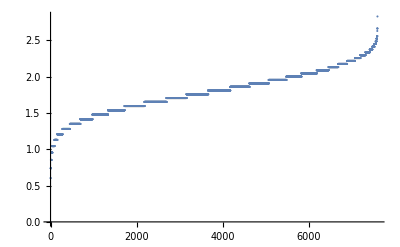

```mathematica
ListPlot[Sort[%]]
```

```mathematica
Select[Range[Length[pl]],IsomorphicGraphQ[Graph[plantri[[1]]],Graph[pl[[#]]]]&]
```

{4198}

```mathematica
VertexCount[Graph[plantri[[1]]]]
```

12

```mathematica
N[Deg[Graph[plantri[[1]]]]]
```

0.

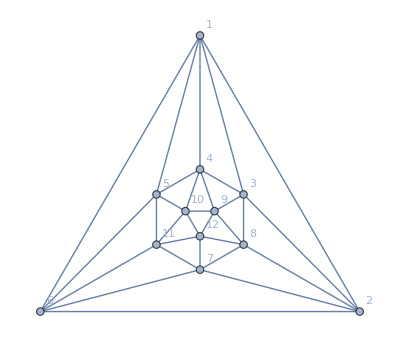

```mathematica
Graph[pl[[4198]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
ff=FindFullFormula[Graph[plantri[[1]]]];
```

```mathematica
BaseGenerators[ff]
```

$Aborted

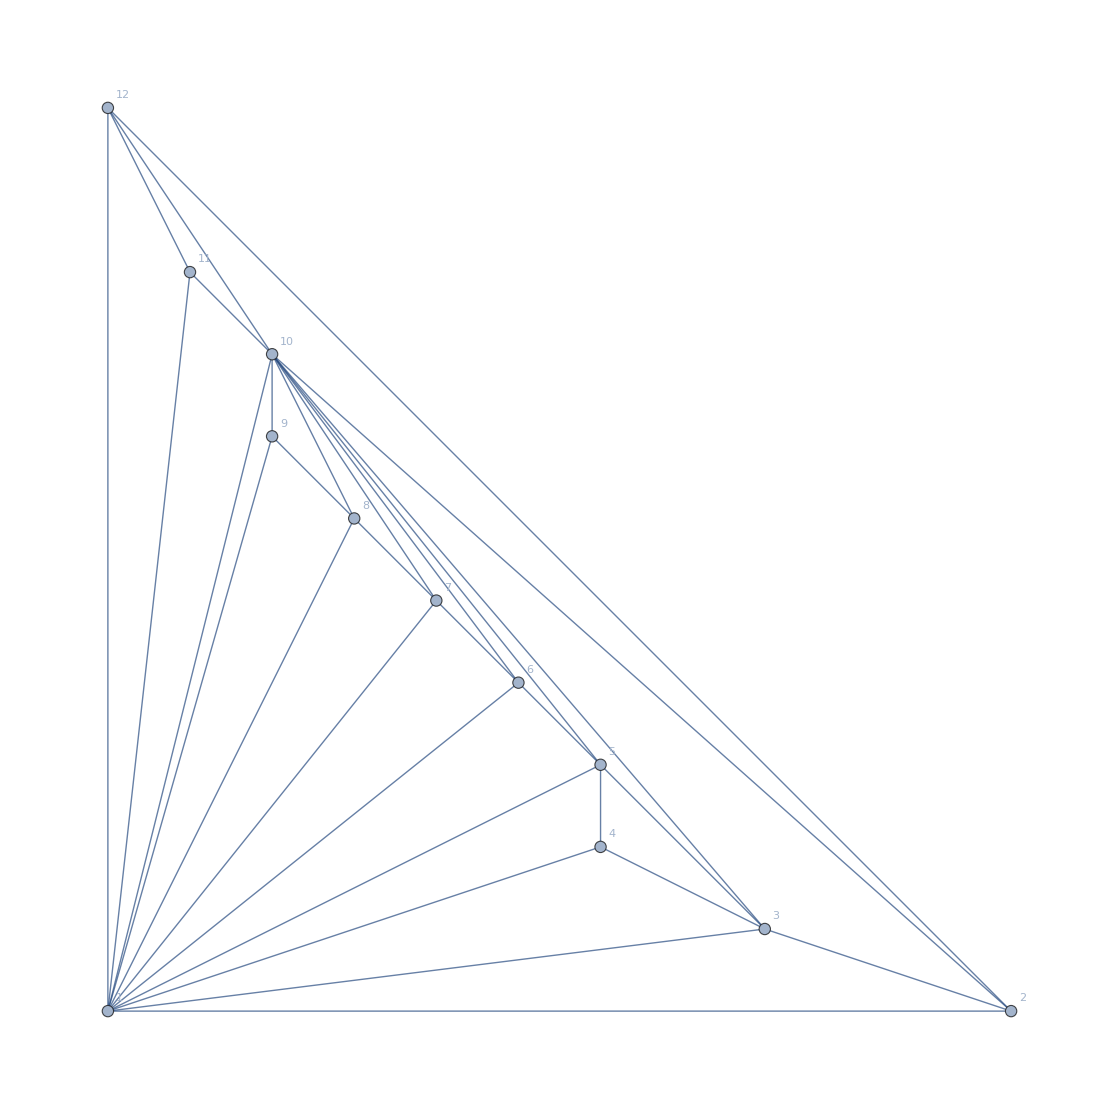

```mathematica
Graph[pl[[2006]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

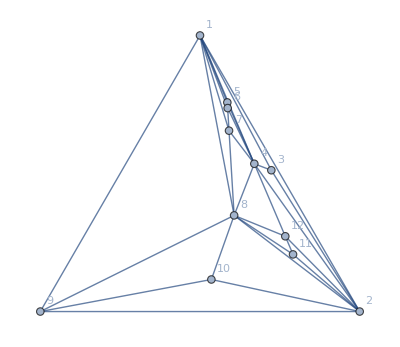

```mathematica
Graph[pl[[1]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

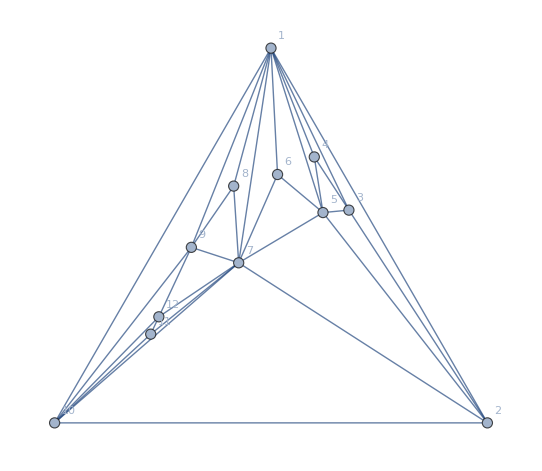

```mathematica
Graph[pl[[17]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
dd=(count=2000;Monitor[
Table[count++;With[{formula=FindFullFormula[Graph[edges]]},
Length[Select[Sort[Tally[Map[PartitionType2[ #]&,formula]]],Length[#[[1]]]==4&]]
],{edges,Take[pl,{2001,2500}]}],
count])
```

$Aborted

```mathematica
CloseAll[]
```

{}

```mathematica
Select[pl,
With[{formula=FindFullFormula[Graph[#]]},
Length[Select[Sort[Tally[Map[PartitionType2[ #]&,formula]]],Length[#[[1]]]==4&]]>=4
]&]
```

{{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,2<->3,2<->9,2<->10,3<->4,3<->10,4<->5,4<->10,5<->6,5<->10,6<->7,6<->10,7<->8,7<->10,8<->9,8<->10,9<->10},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,2<->3,2<->9,3<->4,3<->5,3<->9,3<->10,4<->5,5<->6,5<->10,6<->7,6<->10,7<->8,7<->10,8<->9,8<->10,9<->10},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->7,2<->8,3<->4,3<->8,3<->9,3<->10,4<->5,4<->10,5<->6,5<->8,5<->9,5<->10,6<->7,6<->8,7<->8,8<->9,9<->10}}

```mathematica
Sort[Tally[Map[PartitionType2[ #]&,FindFullFormula[Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->7,2<->8,3<->4,3<->8,3<->9,3<->10,4<->5,4<->10,5<->6,5<->8,5<->9,5<->10,6<->7,6<->8,7<->8,8<->9,9<->10}]]]]]
```

{{{4,3,3},1},{{3,3,2,2},16},{{3,3,3,1},4},{{4,2,2,2},1},{{4,3,2,1},6},{{2,2,2,2,2},22},{{3,2,2,2,1},108},{{3,3,2,1,1},48},{{4,2,2,1,1},11},{{4,3,1,1,1},2},{{2,2,2,2,1,1},242},{{3,2,2,1,1,1},204},{{3,3,1,1,1,1},12},{{4,2,1,1,1,1},7},{{2,2,2,1,1,1,1},330},{{3,2,1,1,1,1,1},80},{{4,1,1,1,1,1,1},1},{{2,2,1,1,1,1,1,1},138},{{3,1,1,1,1,1,1,1},8},{{2,1,1,1,1,1,1,1,1},21},{{1,1,1,1,1,1,1,1,1,1},1}}

```mathematica
Sort[Tally[Map[PartitionType2[ #]&,FindFullFormula[Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,2<->3,2<->9,3<->4,3<->5,3<->9,3<->10,4<->5,5<->6,5<->10,6<->7,6<->10,7<->8,7<->10,8<->9,8<->10,9<->10}]]]]]
```

{{{3,3,2,2},9},{{3,3,3,1},1},{{4,2,2,2},1},{{4,3,2,1},1},{{2,2,2,2,2},19},{{3,2,2,2,1},95},{{3,3,2,1,1},34},{{4,2,2,1,1},5},{{4,3,1,1,1},1},{{2,2,2,2,1,1},191},{{3,2,2,1,1,1},211},{{3,3,1,1,1,1},15},{{4,2,1,1,1,1},5},{{2,2,2,1,1,1,1},288},{{3,2,1,1,1,1,1},104},{{4,1,1,1,1,1,1},1},{{2,2,1,1,1,1,1,1},132},{{3,1,1,1,1,1,1,1},12},{{2,1,1,1,1,1,1,1,1},21},{{1,1,1,1,1,1,1,1,1,1},1}}

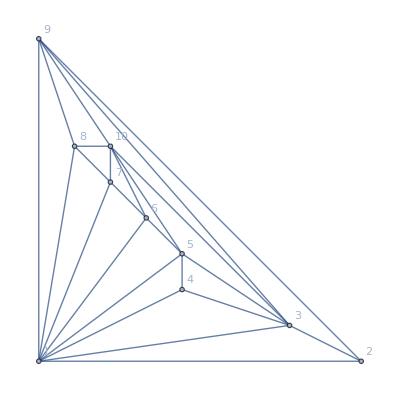

```mathematica
Graph[{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,2<->3,2<->9,3<->4,3<->5,3<->9,3<->10,4<->5,5<->6,5<->10,6<->7,6<->10,7<->8,7<->10,8<->9,8<->10,9<->10},GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```